# Discrete Fourier solutions

## Programming techniques

## Create a time series

### Typed from student sheet

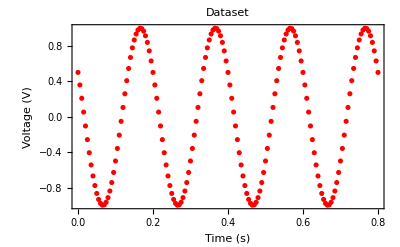

```mathematica
numpt=161;  dt=0.005;
T=dt numpt;  f=5;
data=Table[Cos[2 Pi f t+Pi/3],{t,0,T-dt,dt}];
ListPlot[data,PlotRange->All,DataRange->{0,T-dt},PlotStyle->Red,Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Dataset"]
```

### Answers to questions

-Graphics-

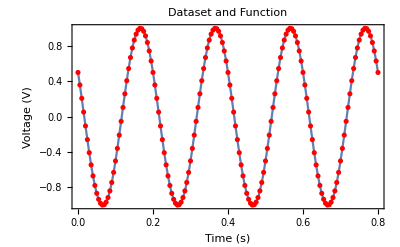

```mathematica
dataplot= ListPlot[data,PlotRange->All,DataRange->{0,T-dt},PlotStyle->Red];
functionplot=Plot[Cos[2 Pi f t+Pi/3],{t,0,T-dt}];
Show[functionplot, dataplot,Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Dataset and Function"]
```

-Graphics-

161

483

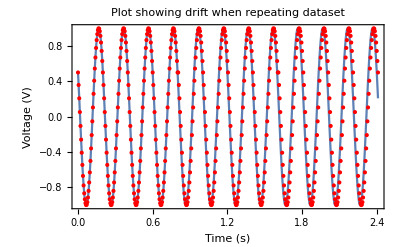

```mathematica
data1=Join[data,data,data];
Length[data]  (* echo original list length for comparison *)
num=Length[data1] (* length of triplicated data list for verification*)
T=dt num;
dataplot=ListPlot[data1,PlotRange->All,DataRange->{0,T-dt},PlotStyle->Red];

functionplot=Plot[Cos[2 Pi f t+Pi/3],{t,0,T-dt}];

Show[functionplot,dataplot,Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Plot showing drift when repeating dataset"]
```

Since the first and last data points coincide, we end up with a duplication of this point when the list is duplicated. Hence, we have a dt drift with each duplication (you should notice a movement of the data points off the function line toward the right end of the plot.

-Graphics-

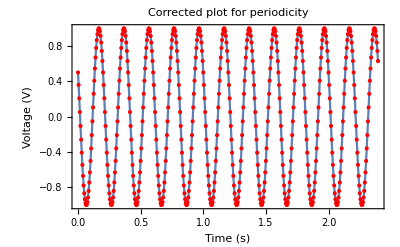

```mathematica
data2=data[[1;;-2]]; (* drop the last data point to maek the set periodic *)
T=dt Length[data2];
datajoin2=Join[data2,data2,data2];
num=Length[datajoin2];
dataplot=ListPlot[datajoin2,PlotRange->All,DataRange->{0,3T- dt},PlotStyle->Red];

functionplot=Plot[Cos[2 Pi f t+Pi/3],{t,0,3T-dt}];

Show[functionplot,dataplot,Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Corrected plot for periodicity"]
```

## Take the Discrete Fourier Transform

### Typed from student sheet

```mathematica
fdata=Fourier[data];
```

### Answers to questions

-Graphics-

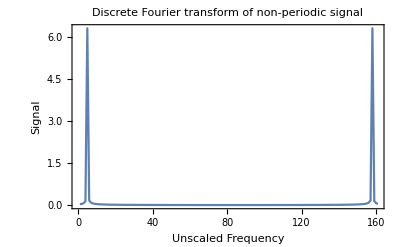

```mathematica
fdata=Fourier[data];
ListLinePlot[Abs[fdata],PlotRange->All,Frame->True,FrameLabel->{"Unscaled Frequency","Signal"},PlotLabel->"Discrete Fourier transform of non-periodic signal"]
```

-Graphics-

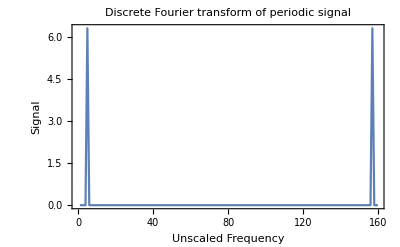

```mathematica
fdata2=Fourier[data2];
ListLinePlot[Abs[fdata2],PlotRange->All,Frame->True,FrameLabel->{"Unscaled Frequency","Signal"},PlotLabel->"Discrete Fourier transform of periodic signal"]
```

You might note that the peaks are a little better defined with the periodic data - look in particular at the width of the base of the peaks. The non-periodic Discrete Fourier plot has broader shoulders.

-Graphics-

```mathematica
Chop[fdata2]
```

{0,0,0,0,3.16228-5.47723 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.16228+5.47723 ⅈ,0,0,0}

-Graphics-

```mathematica
cexp=Cos[ω t]//TrigToExp
sexp = Sin[ω t]//TrigToExp
```

1/2 ⅇ^(-ⅈ t ω)+1/2 ⅇ^(ⅈ t ω)

1/2 ⅈ ⅇ^(-ⅈ t ω)-1/2 ⅈ ⅇ^(ⅈ t ω)

-Graphics-

```mathematica
{cexp[[1]],cexp[[2]]}
Table[sexp[[i]],{i,Length[sexp]}]
Length[cexp]
(* Note that both cos and sin functions have two components that are complex conjugate to each other and correspond to a positive and negative frequency. *)
```

{1/2 ⅇ^(-ⅈ t ω),1/2 ⅇ^(ⅈ t ω)}

{1/2 ⅈ ⅇ^(-ⅈ t ω),-1/2 ⅈ ⅇ^(ⅈ t ω)}

2

-Graphics-

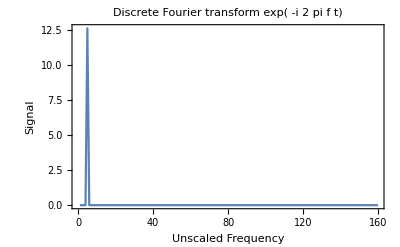

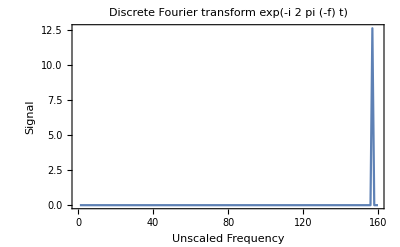

```mathematica
data3=Table[Exp[-I 2 Pi f t],{t,0,T-dt,dt}];
ListLinePlot[Abs[Fourier[data3]],PlotRange->All,Frame->True,FrameLabel->{"Unscaled Frequency","Signal"},PlotLabel->"Discrete Fourier transform exp( -i 2 pi f t)"]

data4=Table[Exp[-I 2 Pi (-f) t],{t,0,T-dt,dt}];
ListLinePlot[Abs[Fourier[data4]],PlotRange->All,Frame->True,FrameLabel->{"Unscaled Frequency","Signal"},PlotLabel->"Discrete Fourier transform exp(-i 2 pi (-f) t)"]
```

## Correct frequency scale and zoom

### Typed from student sheet

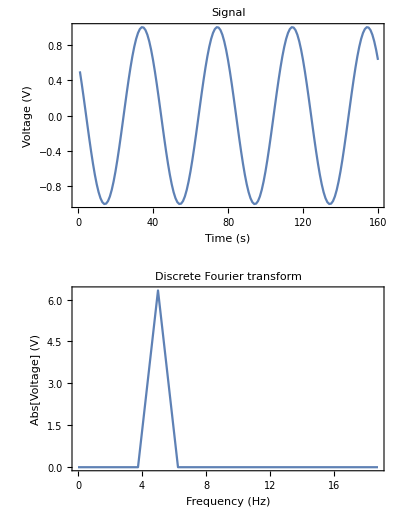

```mathematica
T=dt*Length[data2];
df=1/T; (*frequency step*)
fmax=20;  (*maximum frequency for display*)
nzoom=Round[fmax/df]; (*number of points required from the Fourier list*)
GraphicsGrid[{{ListLinePlot[data2,PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Signal"]},{ListLinePlot[Abs[fdata2⟦1;;nzoom⟧],DataRange->{0,(nzoom-1) df},PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Abs[Voltage] (V)"},PlotLabel->"Discrete Fourier transform"]}}]
```

### Answers to questions

```mathematica
sf=Abs[fdata2[[1;;nzoom]]];
fp=FindPeaks[sf,0,0,1];
(fp[[1,1]]-1)df
(* Find the position of the peak in the list, subtract one to account for the fact that the list position starts counting from one whereas the Fourier transform starts from zero, and multiply by df the account for the step size in the Fourier list, df=1/T i.e. higher resolution obtained by sampling for longer *)
```

5.

-Graphics-

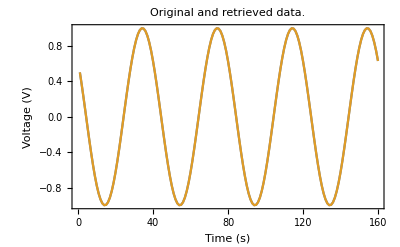

4.66127×10^-16

```mathematica
data2return = InverseFourier[fdata2];
ListLinePlot[{data2,  data2return},Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Original and retrieved data."]
Max[Abs[data2-data2return]]
```

## Superposition of oscillations and noise filtering

### Typed from student sheet

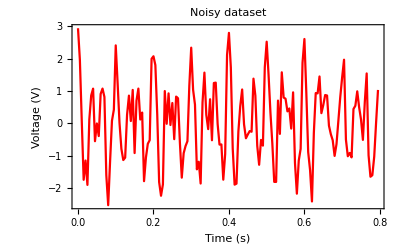

```mathematica
numpt=160;dt=0.005;T=dt numpt;fa3=20;fb3=30;noiselevel=1;
noise=noiselevel RandomReal[{-1,1},numpt];
cleandata=Table[Cos[2 Pi fa3 t]+Cos[2 Pi fb3 t],{t,0,T-dt,dt}];
data=cleandata+noise;
ListLinePlot[data,PlotRange->All,DataRange->{0,T-dt},PlotStyle->Red,Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Noisy dataset"]
```

### Answers to questions

-Graphics-

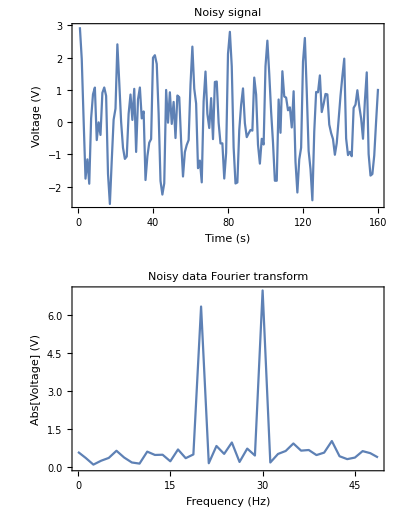

```mathematica
fdata=Fourier[data]; df=1/T; fmax=50;
nzoom=Floor[fmax/df]; (*number of points required from the Fourier list*)
GraphicsGrid[{{ListLinePlot[data,PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Noisy signal"]},{ListLinePlot[Abs[fdata[[1;;nzoom]]],DataRange->{0,(nzoom-1)*df},PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Abs[Voltage] (V)"},PlotLabel->"Noisy data Fourier transform"]}}]
```

-Graphics-

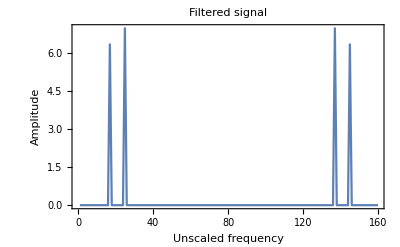

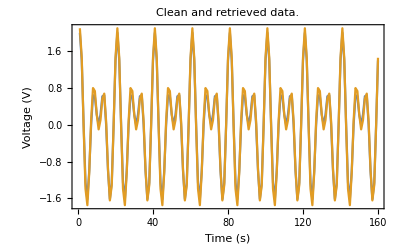

0.1562

```mathematica
ffdata=Threshold[fdata,3];
ListLinePlot[Abs[ffdata],FrameLabel->{"Unscaled frequency","Amplitude"},PlotLabel->"Filtered signal",PlotRange->All,Frame->True]
datareturn = InverseFourier[ffdata];
ListLinePlot[{cleandata,datareturn//Re},Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Clean and retrieved data."]
Max[Abs[cleandata-datareturn]] (* maximum difference (error) *)
```

-Graphics-

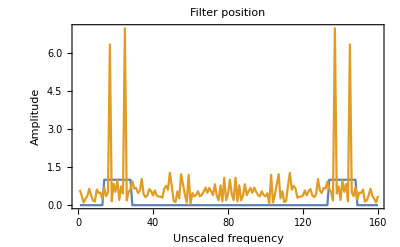

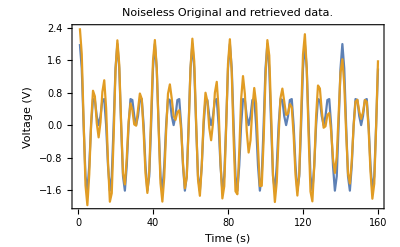

```mathematica
mask=Table[If[Abs[i-21]<8||Abs[i-141]<8,1,0],{i,numpt}];
ListLinePlot[{mask,Abs[fdata]},FrameLabel->{"Unscaled frequency","Amplitude"},PlotLabel->"Filter position",PlotRange->All,Frame->True]
datareturn=InverseFourier[mask fdata];
ListLinePlot[{cleandata,datareturn//Re},Frame->True,FrameLabel->{"Time (s)","Voltage (V)"},PlotLabel->"Noiseless Original and retrieved data.",PlotRange->All,Frame->True]
```

## Study: amplitude modulation

## AM time series and its Fourier transform

### Modulating and Fourier transform

-Graphics-

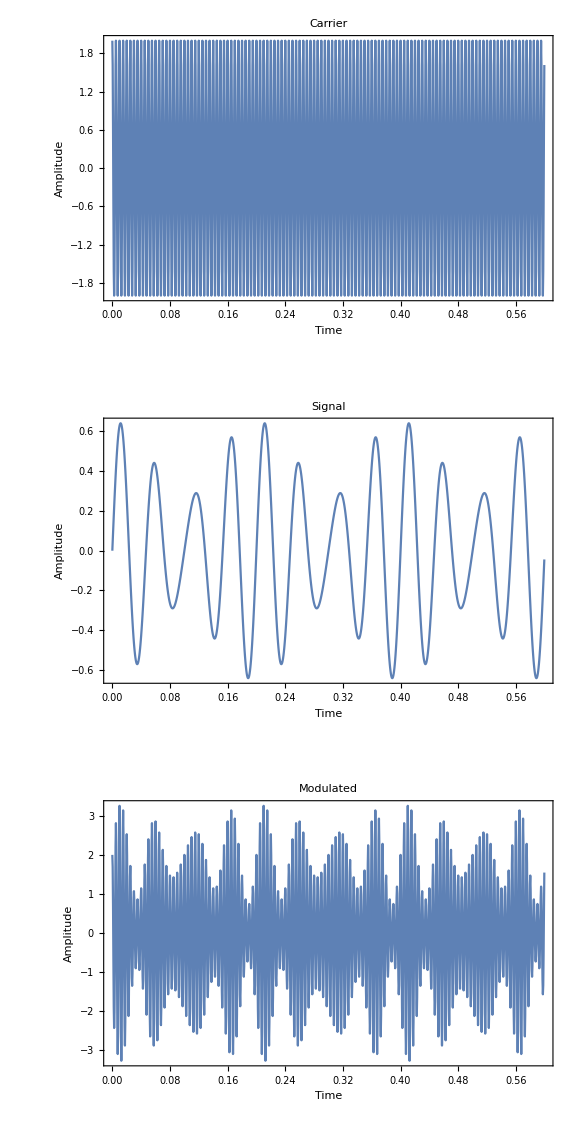

```mathematica
numpt=1200;

fc=200;fm1=20;fm2=25;
ac=2;a1=.45;a2=0.2;
ωc=2*Pi*fc;
ωm1=2*Pi*fm1;
ωm2=2*Pi*fm2;

c[t_]:=ac Cos[ωc*(t)];
m[t_]:=a1 Sin[ωm1*t]+ a2 Sin[ωm2*t];
yA[t_]:=(1+m[t])c[t];

rate=2000.0; (* sampling rate *)
dt=1/rate;
T=numpt*dt;
df=1/T;
ctable=Table[c[t],{t,0,dt(numpt-1),dt}];
mtable=Table[m[t],{t,0,dt(numpt-1),dt}];
yAtable=Table[yA[t],{t,0,dt(numpt-1),dt}];
GraphicsGrid[{{ListPlot[ctable, Joined->True, DataRange->{0,dt(numpt-1)},
Frame->True,FrameLabel->{"Time","Amplitude"},PlotLabel->"Carrier"]},{ListPlot[mtable, Joined->True, DataRange->{0,dt(numpt-1)},
Frame->True,FrameLabel->{"Time","Amplitude"},PlotLabel->"Signal"]},{ListPlot[yAtable, Joined->True, DataRange->{0,dt(numpt-1)},Frame->True,FrameLabel->{"Time","Amplitude"},PlotLabel->"Modulated"]
}},ImageSize->Large]
```

-Graphics-

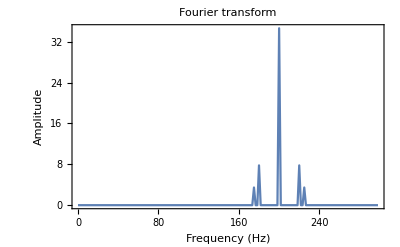

```mathematica
fa=Fourier[yAtable];
fmax=300;
nzoom=Floor[fmax/df];
ListLinePlot[Abs[fa[[1;;nzoom]]],DataRange->{0,(nzoom-1)*df},PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Amplitude"},PlotLabel->"Fourier transform"]
```

-Graphics-

### Identifying peaks analytically

```mathematica
Clear[ac,a1,a2,ωc,ωm1,ωm2]
((1+m[t])c[t]//TrigToExp//Expand)//TraditionalForm
fp=FindPeaks[Abs[fa],0,0,1]
(fp[[1;;5,1]]-1)df (* scaled positive frequencies *) 
(fp[[-5;;-1,1]]-numpt-1)df (* scaled negative frequencies *)
```

1/4 ⅈ a1 ac ⅇ^(-ⅈ t ωc-ⅈ t ωm1)+1/4 ⅈ a1 ac ⅇ^(ⅈ t ωc-ⅈ t ωm1)-1/4 ⅈ a1 ac ⅇ^(ⅈ t ωm1-ⅈ t ωc)-1/4 ⅈ a1 ac ⅇ^(ⅈ t ωc+ⅈ t ωm1)+1/4 ⅈ a2 ac ⅇ^(-ⅈ t ωc-ⅈ t ωm2)+1/4 ⅈ a2 ac ⅇ^(ⅈ t ωc-ⅈ t ωm2)-1/4 ⅈ a2 ac ⅇ^(ⅈ t ωm2-ⅈ t ωc)-1/4 ⅈ a2 ac ⅇ^(ⅈ t ωc+ⅈ t ωm2)+1/2 ac ⅇ^(-ⅈ t ωc)+1/2 ac ⅇ^(ⅈ t ωc)

{{106,3.4641},{109,7.79423},{121,34.641},{133,7.79423},{136,3.4641},{1066,3.4641},{1069,7.79423},{1081,34.641},{1093,7.79423},{1096,3.4641}}

{175.,180.,200.,220.,225.}

{-225.,-220.,-200.,-180.,-175.}

Note that the carrier amplitude acts as an amplifying factor, i.e. it appears multiplying all of these terms.

### Digital filtering

-Graphics-

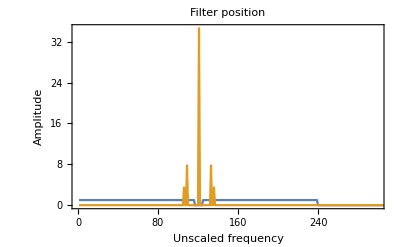

```mathematica
ac=2.;a1=.45;a2=0.2;
ωc=2*Pi*fc;
ωm1=2*Pi*fm1;
ωm2=2*Pi*fm2;

fa=Fourier[yAtable];
filterfc=Floor[fc/df]; (* list position of carrier frequency *)
filter=Table[Piecewise[{{1,i<filterfc-3},{0,i≤ filterfc+4},{1,i<2 filterfc},{0,True}}],{i,numpt}];
ListLinePlot[{ filter,Abs[fa]},PlotRange->{{0,300},All},FrameLabel->{"Unscaled frequency","Amplitude"},PlotLabel->"Filter position",Frame->True]
```

-Graphics-

```mathematica
ffa=filter fa;
rffa=RotateLeft[ffa, filterfc];
```

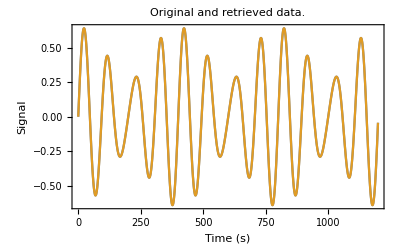

```mathematica
ListLinePlot[{mtable, (2/ac) InverseFourier[rffa]//Re},Frame->True,FrameLabel->{"Time (s)","Signal"},PlotLabel->"Original and retrieved data.",PlotRange->All,Frame->True]
```

With inverse Fourier applied, and the ac factor taken into account, there is a factor of two between our original and recovered signal. This comes from the fact that e have lost half of our signal when we filtered away the negative frequency components. Multiply our recovered signal by two to account for this. Alternatively, you could make filter that drop the positive and negative carrier frequencies and retains everything else. This should then return a match for the original signal.

## Advanced problem

## Radio demodulation technique theory

```mathematica
Cos[w t]^2//TrigReduce

(* Measuring the square of a sinusoidal signal creates a second harmonic signal and a DC term.  *)
```

1/2 (1+Cos[2 t w])

```mathematica
ac=.;a1=.;a2=.;ωc=.;ωm1=.;ωm2=.
c[t_]:=ac Cos[ωc*t];
m[t_]:=a1 Sin[ωm1*t]+ a2 Sin[ωm2*t];

sig[t_]:=(1+m[t])c[t]
sig2=sig[t]^2//TrigToExp//Expand
sig2//Length
Select[sig2,Length[Position[#,ωc]]==0&]//FullSimplify
```

ac^2/2+(a1^2 ac^2)/4+(a2^2 ac^2)/4+1/4 ac^2 ⅇ^(-2 ⅈ t ωc)+1/8 a1^2 ac^2 ⅇ^(-2 ⅈ t ωc)+1/8 a2^2 ac^2 ⅇ^(-2 ⅈ t ωc)+1/4 ac^2 ⅇ^(2 ⅈ t ωc)+1/8 a1^2 ac^2 ⅇ^(2 ⅈ t ωc)+1/8 a2^2 ac^2 ⅇ^(2 ⅈ t ωc)+1/2 ⅈ a1 ac^2 ⅇ^(-ⅈ t ωm1)-1/2 ⅈ a1 ac^2 ⅇ^(ⅈ t ωm1)-1/8 a1^2 ac^2 ⅇ^(-2 ⅈ t ωm1)-1/8 a1^2 ac^2 ⅇ^(2 ⅈ t ωm1)+1/4 ⅈ a1 ac^2 ⅇ^(-2 ⅈ t ωc-ⅈ t ωm1)+1/4 ⅈ a1 ac^2 ⅇ^(2 ⅈ t ωc-ⅈ t ωm1)-1/4 ⅈ a1 ac^2 ⅇ^(-2 ⅈ t ωc+ⅈ t ωm1)-1/4 ⅈ a1 ac^2 ⅇ^(2 ⅈ t ωc+ⅈ t ωm1)-1/16 a1^2 ac^2 ⅇ^(-2 ⅈ t ωc-2 ⅈ t ωm1)-1/16 a1^2 ac^2 ⅇ^(2 ⅈ t ωc-2 ⅈ t ωm1)-1/16 a1^2 ac^2 ⅇ^(-2 ⅈ t ωc+2 ⅈ t ωm1)-1/16 a1^2 ac^2 ⅇ^(2 ⅈ t ωc+2 ⅈ t ωm1)+1/2 ⅈ a2 ac^2 ⅇ^(-ⅈ t ωm2)-1/2 ⅈ a2 ac^2 ⅇ^(ⅈ t ωm2)-1/8 a2^2 ac^2 ⅇ^(-2 ⅈ t ωm2)-1/8 a2^2 ac^2 ⅇ^(2 ⅈ t ωm2)+1/4 ⅈ a2 ac^2 ⅇ^(-2 ⅈ t ωc-ⅈ t ωm2)+1/4 ⅈ a2 ac^2 ⅇ^(2 ⅈ t ωc-ⅈ t ωm2)-1/4 a1 a2 ac^2 ⅇ^(-ⅈ t ωm1-ⅈ t ωm2)-1/8 a1 a2 ac^2 ⅇ^(-2 ⅈ t ωc-ⅈ t ωm1-ⅈ t ωm2)-1/8 a1 a2 ac^2 ⅇ^(2 ⅈ t ωc-ⅈ t ωm1-ⅈ t ωm2)+1/4 a1 a2 ac^2 ⅇ^(ⅈ t ωm1-ⅈ t ωm2)+1/8 a1 a2 ac^2 ⅇ^(-2 ⅈ t ωc+ⅈ t ωm1-ⅈ t ωm2)+1/8 a1 a2 ac^2 ⅇ^(2 ⅈ t ωc+ⅈ t ωm1-ⅈ t ωm2)-1/4 ⅈ a2 ac^2 ⅇ^(-2 ⅈ t ωc+ⅈ t ωm2)-1/4 ⅈ a2 ac^2 ⅇ^(2 ⅈ t ωc+ⅈ t ωm2)+1/4 a1 a2 ac^2 ⅇ^(-ⅈ t ωm1+ⅈ t ωm2)+1/8 a1 a2 ac^2 ⅇ^(-2 ⅈ t ωc-ⅈ t ωm1+ⅈ t ωm2)+1/8 a1 a2 ac^2 ⅇ^(2 ⅈ t ωc-ⅈ t ωm1+ⅈ t ωm2)-1/4 a1 a2 ac^2 ⅇ^(ⅈ t ωm1+ⅈ t ωm2)-1/8 a1 a2 ac^2 ⅇ^(-2 ⅈ t ωc+ⅈ t ωm1+ⅈ t ωm2)-1/8 a1 a2 ac^2 ⅇ^(2 ⅈ t ωc+ⅈ t ωm1+ⅈ t ωm2)-1/16 a2^2 ac^2 ⅇ^(-2 ⅈ t ωc-2 ⅈ t ωm2)-1/16 a2^2 ac^2 ⅇ^(2 ⅈ t ωc-2 ⅈ t ωm2)-1/16 a2^2 ac^2 ⅇ^(-2 ⅈ t ωc+2 ⅈ t ωm2)-1/16 a2^2 ac^2 ⅇ^(2 ⅈ t ωc+2 ⅈ t ωm2)

45

1/2 ac^2 (1+a1 Sin[t ωm1]+a2 Sin[t ωm2])^2

## Radio demodulation

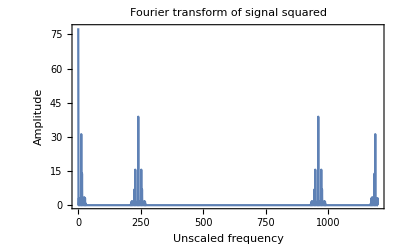

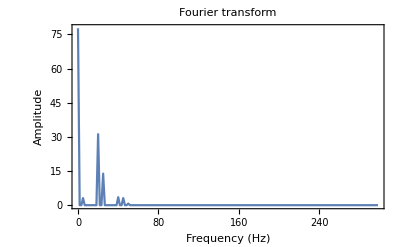

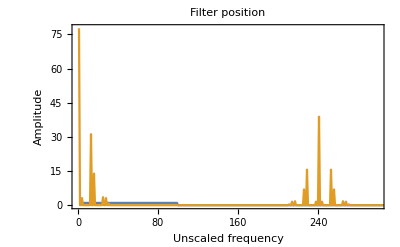

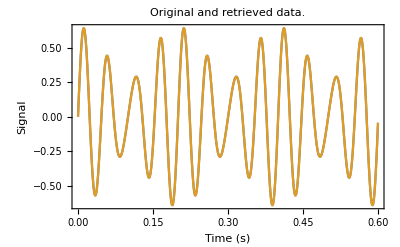

```mathematica
ac=2;
fa2=Fourier[yAtable^2];
ListLinePlot[Abs[fa2],PlotRange->All,FrameLabel->{"Unscaled frequency","Amplitude"},Frame->True,PlotLabel->"Fourier transform of signal squared"]

fmax=300;
nzoom=Floor[fmax/df];
ListLinePlot[Abs[fa2[[1;;nzoom]]],DataRange->{0,(nzoom-1)*df},PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Amplitude"},PlotLabel->"Fourier transform"]

filtermax=100;
filter=Table[Piecewise[{{1,i<filtermax},{0,i<Length[yAtable]-filtermax},{1,i≥Length[yAtable]-filtermax}}],{i,Length[yAtable]}];

ListLinePlot[{ filter,Abs[fa2]},PlotRange->{{0,300},All},FrameLabel->{"Unscaled frequency","Amplitude"},PlotLabel->"Filter position",Frame->True]

inv2=Re[Sqrt[(2/ac^2) InverseFourier[filter fa2]]];

ListPlot[{mtable, inv2-Mean[inv2]},Joined->True, DataRange->{0,dt (numpt-1)},Frame->True,FrameLabel->{"Time (s)","Signal"},PlotLabel->"Original and retrieved data.",PlotRange->All,Frame->True]
```